```mathematica
(* Find the optimal proportion of helper of fully coordinated population *)
```

```mathematica
WCord[q_]= Simplify[(1-θ) (1-q)(1-ϵ +ϵ q/l+ϵ(l-1) QCord/l)]
```

((-1+q) (l+(q-QCord) ϵ+l (-1+QCord) ϵ) (-1+θ))/l

```mathematica
Solve[WCord'[q]==0, q]
```

{{q→(-l+ϵ+l ϵ+QCord ϵ-l QCord ϵ)/(2 ϵ)}}

```mathematica
(* Find q*_FC *)
```

```mathematica
Solve[q==(-l+ϵ+l ϵ+q ϵ-l q ϵ)/(2 ϵ), q] (* Replace QCord with q *)
```

{{q→(-l+ϵ+l ϵ)/((1+l) ϵ)}}

```mathematica
(* Finding the invading condition for a fully random founder *)
```

```mathematica
WRandInv[q_]:= Simplify[(1-q) (1-ϵ-ϵ q/l/m+ϵ q/l+ϵ QCord (l-1)/l)]
```

```mathematica
(* Assuming invader using q*_FC *)
```

```mathematica
QCord= (-l+ϵ+l ϵ)/((1+l) ϵ); Simplify[WRandInv[(-l+ϵ+l ϵ)/((1+l) ϵ)]]
```

(l (1+m-ϵ)-ϵ)/((1+l)^2 m ϵ)

```mathematica
QCord= (-l+ϵ+l ϵ)/((1+l) ϵ); Simplify[WCord[(-l+ϵ+l ϵ)/((1+l) ϵ)]]
```

-(l (-1+θ))/((1+l)^2 ϵ)

```mathematica
(* Find critical invading condition *)
```

```mathematica
Simplify[Solve[(l (1+m-ϵ)-ϵ)/((1+l)^2 m ϵ)==-(l (-1+θ))/((1+l)^2 ϵ), ϵ]]
```

{{ϵ→(l+l m θ)/(1+l)}}

```mathematica
(* Plotting *)
```

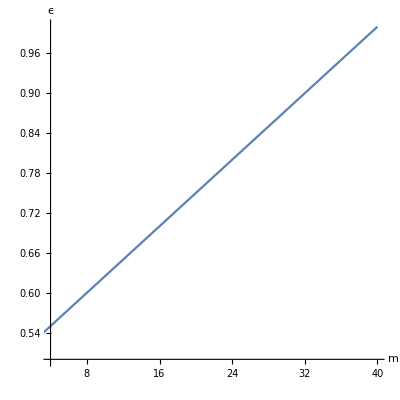

```mathematica
l=1; θ= 0.025; 
Plot[{(l+l m θ)/(1+l)}, {m, 1, 40}, PlotRange-> {{4,40},{0.5, 1}}, AxesLabel->{m,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

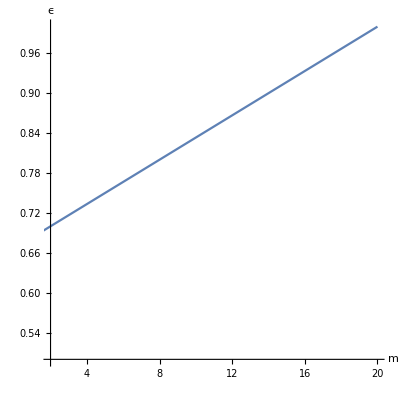

```mathematica
l=2; θ= 0.025; 
Plot[{(l+l m θ)/(1+l)}, {m, 1, 40}, PlotRange-> {{2,20},{0.5, 1}}, AxesLabel->{m,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

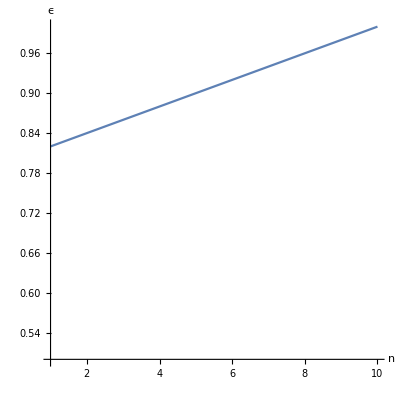

```mathematica
l=4; θ= 0.025; 
Plot[{(l+l m θ)/(1+l)}, {m, 1, 40}, PlotRange-> {{1,10},{0.5, 1}}, AxesLabel->{n,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

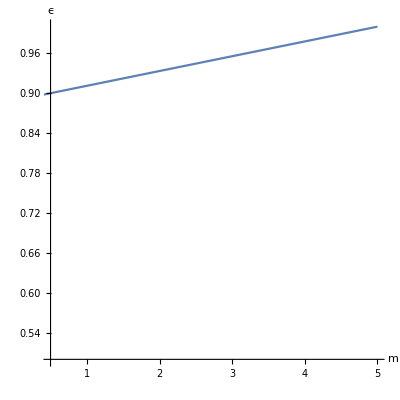

```mathematica
l=8; θ= 0.025; 
Plot[{(l+l m θ)/(1+l)}, {m, 0, 40}, PlotRange-> {{0.5,5},{0.5, 1}}, AxesLabel->{m,ϵ}, PlotLegends->Automatic, AspectRatio->1]
```

```mathematica
Clear[QRand, QCord, l,θ,ϵ,m]
```